```mathematica
Item[KeyEvent["m",Modifiers->{Control}],FrontEndExecute[{FrontEnd`SelectionMove[FrontEnd`SelectedNotebook[],All,Cell],FrontEnd`FrontEndToken["Clear"]}]],
```

```mathematica
(*Let's calculate m_infinity and n_infinity*)
aM := (0.1*(25-V[t]))/(Exp[(0.1*(25-V[t]))]-1)
bM := 4*Exp[-V[t]/18]
mInf := (aM)/(aM+bM)
```

```mathematica
aN:= (0.1*(10-V[t]))/(Exp[(0.1*(10-V[t]))]-1)
```

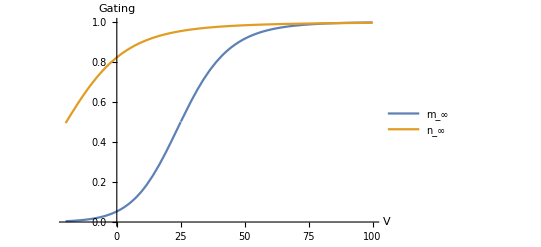

```mathematica
bN := 0.125*Exp[-V[t]/80]
nInf:= (aN)/(aN+bN)
tauN := 1/(aN+bN)
(* Now we can plot these gating variables *)

Plot[{mInf,nInf},{V[t], -20, 100}, PlotLegends->{Subscript[m, Infinity], Subscript[n, Infinity]}, AxesLabel->{V, "Gating"}]
```

```mathematica
gNa := 120
gK := 36
gL := 0.3
eNa := 115
eK := -12
eL := 10.6
```

```mathematica
fastFast=NDSolve[{V'[t]==-gNa*nn[t]^3*0.596*(V[t]-eNa)-gK * 0.3176^4(V[t]-eK)-gL(V[t]-eL),nn'[t]==aM*(1-nn[t])-bM*nn[t],V[0]==1, nn[0]==0.1},{V, nn},{t,30}]
```

{{V→InterpolatingFunction[{{0., 30.}}, <>],nn→InterpolatingFunction[{{0., 30.}}, <>]}}

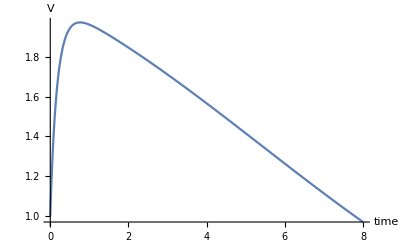

Unset::write: Tag Function in (0&)[t] is Protected.

```mathematica
Plot[ V[t]/.fastFast,{t,0,8}, AxesLabel->{"time", V}]
```

```mathematica
fc1 := aM*(1-x)-bM*x
fc2:=-gNa*x^3*0.596*(V[t]-eNa)-gK * 0.3176^4(V[t]-eK)-gL(V[t]-eL)
```

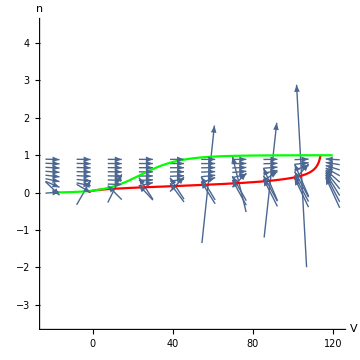

```mathematica
Show[VectorPlot[{fc2,fc1},{V[t],-20,120},{x,0,1},Epilog->{PointSize[0.03]},Frame->False,Axes->True,VectorScale->{0.05,1,None},VectorPoints->Coarse,ImageSize->Medium],ContourPlot[{fc2==0,fc1==0},{V[t],-20,120},{x,0,1},ContourStyle->{Red, Green}], AxesLabel-> {V, n}]
```

```mathematica
Export["/Users/farissbahi/Desktop/PHY513/PHY 513 - Final Project/fastFast_nullc.png",%594,"PNG"]
```

/Users/farissbahi/Desktop/PHY513/PHY 513 - Final Project/fastFast_nullc.png

Unset::norep: Assignment on V for V[t] not found.

```mathematica
fastSlow=NDSolve[{V'[t]==50-gNa*mInf^3(0.8-nn[t])(V[t]-eNa)-gK * nn[t]^4(V[t]-eK)-gL(V[t]-eL),nn'[t]==aN*(1-nn[t])-bN*nn[t],V[0]==50, nn[0]==0.3},{V, nn},{t,30}]
```

{{V→InterpolatingFunction[{{0., 30.}}, <>],nn→InterpolatingFunction[{{0., 30.}}, <>]}}

```mathematica
(* Plot action potential *)
```

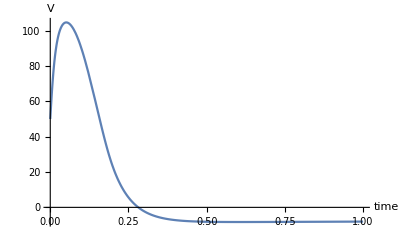

```mathematica
Plot[ V[t]/.fastSlow,{t,0,1}, AxesLabel->{"time", V}]
```

```mathematica
Export["/Users/farissbahi/Desktop/PHY513/PHY 513 - Final Project/zero_ext_actionpotential.png",%119,"PNG"]
```

/Users/farissbahi/Desktop/PHY513/PHY 513 - Final Project/zero_ext_actionpotential.png

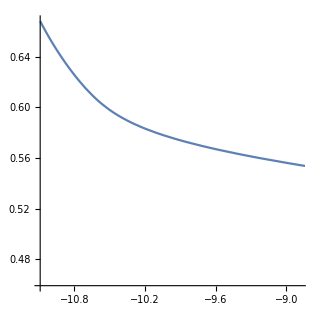

```mathematica
ParametricPlot[Evaluate[{V[t],nn[t]}/.fastSlow],{t,0,10}, AspectRatio-> 1]
```

```mathematica
(* Define null-clines of fast-slow *)
```

```mathematica
null1 := (aN*(1-1.5*x)-bN*1.5*x)
null2:=50-gNa*mInf^3(0.8-x)(V[t]-eNa)-gK * (x)^4(V[t]-eK)-gL(V[t]-eL)
null2Sol:= NSolve[null2==0,V[t]]
```

```mathematica
(* Plot null-clines of fast-slow in vector field*)
(* ,Point[{x,V[t]}/.First[NSolve[{null1==0,null2==0}]]] *)
```

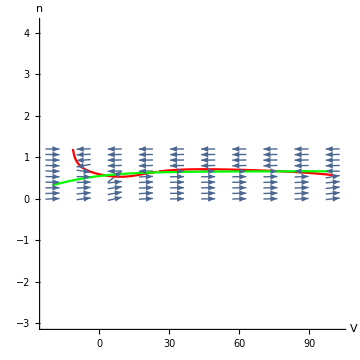

```mathematica
Show[VectorPlot[{null2,null1},{V[t],-20,100},{x,0,1.2},Epilog->{PointSize[0.03]},Frame->False,Axes->True,VectorScale->{0.05,1,None},VectorPoints->Coarse,ImageSize->Medium],ContourPlot[{null2==0,null1==0},{V[t],-20,100},{x,0,1.2},ContourStyle->{Red, Green}], AxesLabel-> {V, n}]
```

```mathematica
(* Now we move on to our further simplified model * )
```

```mathematica
generalCubic=NDSolve[{V'[t]== 100(1+V[t]*(1-V[t])*(V[t]-0.1)-nn[t]),nn'[t]==V[t]-0.5*nn[t], V[0]==0.5,nn[0]==0},{V, nn},{t,10}]
```

{{V→InterpolatingFunction[{{0., 10.}}, <>],nn→InterpolatingFunction[{{0., 10.}}, <>]}}

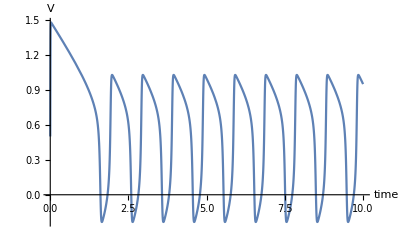

```mathematica
Plot[ V[t]/.generalCubic,{t,0,10}, AxesLabel->{"time", V}]
```

```mathematica
nc1 := V[t]-0.5*x
nc2:=100(1+V[t]*(1-V[t])*(V[t]-0.1)-x)
```

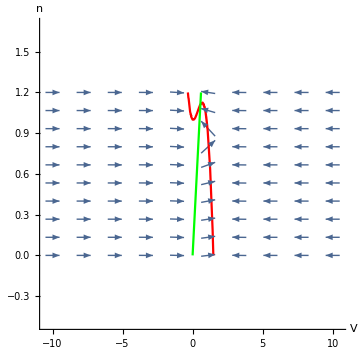

```mathematica
Show[VectorPlot[{nc2,nc1},{V[t],-10,10},{x,0,1.2},Epilog->{PointSize[0.03]},Frame->False,Axes->True,VectorScale->{0.05,1,None},VectorPoints->Coarse,ImageSize->Medium],ContourPlot[{nc2==0,nc1==0},{V[t],-10,10},{x,0,1.2},ContourStyle->{Red, Green}], AxesLabel-> {V, n}]
```

```mathematica
Export["/Users/farissbahi/Desktop/PHY513/PHY 513 - Final Project/sustained_nagumo_nullc.png",%540,"PNG"]
```

/Users/farissbahi/Desktop/PHY513/PHY 513 - Final Project/sustained_nagumo_nullc.png

```mathematica
Export["/Users/farissbahi/Desktop/PHY513/PHY 513 - Final Project/nullc_naguro.png",%528,"PNG"]
```

/Users/farissbahi/Desktop/PHY513/PHY 513 - Final Project/nullc_naguro.png

```mathematica
(*analytical*)

fixedPt = Solve[{V((1-V)(V-0.1)-2)+5==0,n==2V},{V,n}]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{Re[V→-0.277825-1.71545 ⅈ],Re[n→-0.55565-3.4309 ⅈ]},{Re[V→-0.277825+1.71545 ⅈ],Re[n→-0.55565+3.4309 ⅈ]},{Re[V→1.65565],Re[n→3.3113]}}

Solve::ivar: 30 is not a valid variable.

Solve[{i+(-2+(1-V) (-0.1+V)) V[i]==0,n==2 V},{V,n},{i,30}]

```mathematica
Plot[ 5((V/.Solve[{V((1-V)(V-0.1)-2)+i==0,n==2V},{V,n}])^2-22(V/.Solve[{V((1-V)(V-0.1)-2)+i==0,n==2V},{V,n}])+1)+100,{i,0,8}, AxesLabel->{"I_ext", "Determinant"}]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

$Aborted